```mathematica
rota[t_,n_,n1_,n2_]:=Module[{mat},mat=IdentityMatrix[n];mat[[n1]][[n1]]=Cos[t];mat[[n2]][[n2]]=Cos[t];mat[[n1]][[n2]]=-Sin[t];mat[[n2]][[n1]]=Sin[t];mat]
```

```mathematica
rota[t0102,2,1,2]//MatrixForm
```

(Cos[t0102] | -Sin[t0102]
Sin[t0102] | Cos[t0102])

```mathematica
r01[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
mat[[;;,1]]]
```

```mathematica
r01[t,2]//MatrixForm
```

(Cos[t[1,1]]
Sin[t[1,1]])

```mathematica
D[RealAbs[r01[t,2][[1]]],t[1,1]]^2+D[RealAbs[r01[t,2][[2]]],t[1,1]]^2
```

(Cos[t[1,1]]^2 Sin[t[1,1]]^2)/RealAbs[Cos[t[1,1]]]^2+(Cos[t[1,1]]^2 Sin[t[1,1]]^2)/RealAbs[Sin[t[1,1]]]^2

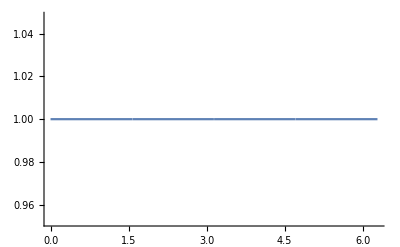

```mathematica
Plot[(Cos[t[1,1]]^2 Sin[t[1,1]]^2)/RealAbs[Cos[t[1,1]]]^2+(Cos[t[1,1]]^2 Sin[t[1,1]]^2)/RealAbs[Sin[t[1,1]]]^2,{t[1,1],0,2Pi}]
```

```mathematica
r01[t,3]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]]
Cos[t[1,2]] Sin[t[1,1]]
Sin[t[1,2]])

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,3][[1]]],t[1,1]]^2+D[RealAbs[r01[t,3][[1]]],t[1,2]]^2]],{t[1,1],t[1,2]}]
```

{1,{t[1,1]→-24 π,t[1,2]→-(11 π)/2}}

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,3][[2]]],t[1,1]]^2+D[RealAbs[r01[t,3][[2]]],t[1,2]]^2]],{t[1,1],t[1,2]}]
```

{1,{t[1,1]→-(49 π)/2,t[1,2]→-(11 π)/2}}

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,3][[3]]],t[1,1]]^2+D[RealAbs[r01[t,3][[3]]],t[1,2]]^2]],{t[1,1],t[1,2]}]
```

{1,{t[1,1]→0,t[1,2]→0}}

```mathematica
r01[t,4]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]]
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]]
Cos[t[1,3]] Sin[t[1,2]]
Sin[t[1,3]])

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,4][[1]]],t[1,1]]^2+D[RealAbs[r01[t,4][[1]]],t[1,2]]^2+D[RealAbs[r01[t,4][[1]]],t[1,3]]^2]],{t[1,1],t[1,2],t[1,3]}]
```

{1,{t[1,1]→-(97 π)/2,t[1,2]→-10 π,t[1,3]→-36 π}}

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,4][[2]]],t[1,1]]^2+D[RealAbs[r01[t,4][[2]]],t[1,2]]^2+D[RealAbs[r01[t,4][[2]]],t[1,3]]^2]],{t[1,1],t[1,2],t[1,3]}]
```

{1,{t[1,1]→-(97 π)/2,t[1,2]→-(21 π)/2,t[1,3]→-36 π}}

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,4][[3]]],t[1,1]]^2+D[RealAbs[r01[t,4][[3]]],t[1,2]]^2+D[RealAbs[r01[t,4][[3]]],t[1,3]]^2]],{t[1,1],t[1,2],t[1,3]}]
```

{1,{t[1,1]→-9/5,t[1,2]→-(49 π)/2,t[1,3]→-(11 π)/2}}

```mathematica
Maximize[FullSimplify[Sqrt[D[RealAbs[r01[t,4][[4]]],t[1,1]]^2+D[RealAbs[r01[t,4][[4]]],t[1,2]]^2+D[RealAbs[r01[t,4][[4]]],t[1,3]]^2]],{t[1,1],t[1,2],t[1,3]}]
```

{1,{t[1,1]→0,t[1,2]→0,t[1,3]→0}}

```mathematica
r02[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
Do[mat=mat.rota[t[2,i-1],n,2,i],{i,3,n}];
mat[[;;,1;;2]]]
```

```mathematica
r02[t,3]/.t[1,2]->0//MatrixForm
```

(Cos[t[1,1]] | -Cos[t[2,2]] Sin[t[1,1]]
Sin[t[1,1]] | Cos[t[1,1]] Cos[t[2,2]]
0 | Sin[t[2,2]])

```mathematica
r03[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
Do[mat=mat.rota[t[2,i-1],n,2,i],{i,3,n}];
Do[mat=mat.rota[t[3,i-1],n,3,i],{i,4,n}];
mat[[;;,1;;3]]]
```

```mathematica
r03[t,4]//MatrixForm
```

(Cos[t[1,1]] Cos[t[1,2]] Cos[t[1,3]] | Cos[t[2,3]] (-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,1]] Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[3,3]] (-Cos[t[1,1]] Cos[t[2,2]] Sin[t[1,2]]+Sin[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,1]] Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]-(-Cos[t[2,2]] Sin[t[1,1]]-Cos[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]]
Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,1]] | Cos[t[2,3]] (Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]])-Cos[t[1,2]] Sin[t[1,1]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[3,3]] (-Cos[t[2,2]] Sin[t[1,1]] Sin[t[1,2]]-Cos[t[1,1]] Sin[t[2,2]])+(-Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,1]] Sin[t[1,3]]-(Cos[t[1,1]] Cos[t[2,2]]-Sin[t[1,1]] Sin[t[1,2]] Sin[t[2,2]]) Sin[t[2,3]]) Sin[t[3,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]] Sin[t[2,2]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | Cos[t[1,2]] Cos[t[2,2]] Cos[t[3,3]]+(-Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,2]] Sin[t[2,3]]) Sin[t[3,3]]
Sin[t[1,3]] | Cos[t[1,3]] Sin[t[2,3]] | Cos[t[1,3]] Cos[t[2,3]] Sin[t[3,3]])

```mathematica
r04[t_,n_]:=Module[{mat},mat=IdentityMatrix[n];
Do[mat=mat.rota[t[1,i-1],n,1,i],{i,2,n}];
Do[mat=mat.rota[t[2,i-1],n,2,i],{i,3,n}];
Do[mat=mat.rota[t[3,i-1],n,3,i],{i,4,n}];
Do[mat=mat.rota[t[4,i-1],n,4,i],{i,5,n}];
mat[[;;,1;;4]]]
```